Universidad de Jaén. Escuela Politécnica Superior de Jaén.    
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# Notas del Tema 2: Números complejos (15-09-2024)

# Tema 2: El cuerpo de los números reales.

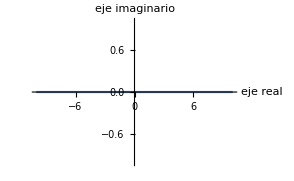
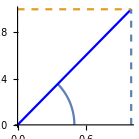
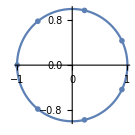
Cuestiones previas.
	¿Dónde encontrar información sobre este tema? La mayoría de libros titulados Análisis, Análisis Matemático, Cálculo o Cálculo Infinitesimal pueden ser útiles para este tema y para muchos otros. También es fácil encontrar en internet apuntes, presentaciones y vídeos de diferentes profesores y universidades que pueden ser de utilidad.
	Lo que aquí se presenta son una notas de carácter informal para ayudar a comprender lo que aparece en los libros y para conocer hasta dónde llegar. Los problemas que hay al final son algunos ejemplos y cada uno debe valorar si son muchos o pocos, y en su caso, buscar más del nivel que considere oportuno. 

1. Necesidad de los números complejos.	
	En el tema anterior hemos visto sucesivas ampliaciones del conjunto de los números, desde los naturales a los reales. 
	Con los números naturales no podíamos resolver las ecuaciones: 
			x+5 = 2 (necesitamos los negativos y ampliamos al conjunto de los enteros)
			2x = 3 (los enteros no son suficientes, necesitamos las fracciones y ampliamos a los números racionales)
			x^2 = 2 (las fracciones no son suficientes, necesitamos los irracionales y ampliamos a los números reales)
			x^2 + 1 =0 (los reales no son suficientes, necesitamos una nueva ampliación)
	Para que tuviese solución, necesitaríamos un número cuyo cuadrado fuese -1. Si suponemos un número ⅈ tal que ⅈ^2=-1, tendríamos que cualquier ecuación de segundo grado, ax^2+bx + c =0, tendría solución. 
	En ocasiones, al utilizar la fórmula para obtener la solución de la ecuación de segundo grado, x= (-b±√(b^2-4ac))/(2a), nos encontramos en el radicando una cantidad negativa. Se podría escribir x = -b/(2a)±(√(4ac-b^2))/(2a) ⅈ, una suma de un número real y un número real por ⅈ. Estos números, así formados, suma de un número real y un número real por ⅈ, serán los números complejos.
	Más aún, el Teorema fundamental del álgebra dice que cualquier ecuación polinómica (con coeficientes reales o complejos) tiene todas sus soluciones en los números complejos. No será necesario, por tanto, ampliar el conjunto de números para que las ecuaciones polinómicas tengan solución.
	
2. Suma y producto. El cuerpo de los números complejos.
	Los números complejos serán de la forma a + bⅈ, con a y b números reales. Los números reales pueden verse como parte de los complejos, serían aquellos en que b=0, es decir, de la forma a+0ⅈ = a.
	Los números reales se representan en una recta. De forma similar, los complejos se podrían representar como puntos en un plano. 
	Los números reales se podrían colocar en el eje horizontal. En el eje vertical colocaríamos el eje imaginario.
	El número complejo a + bⅈ correspondería con el punto (a,b) o con el vector que va desde el punto (0,0) al punto (a,b). Algunos llaman al punto (a,b) el afijo del número complejo a + ⅈ b.
	
	-Graphics-
	
	Las operaciones suma y producto de los reales se extienden a los números complejos y los complejos con la suma y producto vuelven a ser un cuerpo (lo que significa que se facilitan las operaciones). 
	
	(a+ⅈb)+(c+ⅈd) = (a+c) + ⅈ(b+d)
	(a+ⅈb)*(c+ⅈd) = (ac-bd)+ ⅈ (ad+bc) (aquí se utiliza el hecho de que ⅈ^2=-1)
	
	Es fácil comprobar que la suma es asociativa y conmutativa, que el 0=0+0ⅈ es el elemento neutro y que para cada número a+ⅈb su elemento opuesto es (-a-ⅈb).
	Igualmente, es fácil comprobar el producto es asociativo y conmutativo, que el 1 = 1+ 0ⅈ es el elemento unidad y que para cada número a + ⅈb distinto de cero, su inverso es a/(a^2+b^2) - b/(a^2+b^2)ⅈ.
	También es fácil comprobar la propiedad distributiva (podemos sacar factor común). 
	El “truco” para encontrar un inverso o para dividir dos números complejos, es multiplicar y dividir por el conjugado de un número complejo
			(a+ⅈb)/(c+ⅈd)=(a+ⅈb)/(c+ⅈd)(c-ⅈd)/(c-ⅈd)= ((ac+bd)+ⅈ(bc-ad))/(c^2+d^2)=(ac+bd)/(c^2+d^2)+i(bc-ad)/(c^2+d^2)

	El conjugado de un número complejo a + ⅈb es a - ⅈb. Se suele indicar con una línea horizontal sobre el número. Si z = a+ⅈb,  z̄ = a - ⅈb. Algunas propiedades del conjugado son:
	1) OverBar[z+w] = z̄+w̄
	2) OverBar[z*w] = z̄*w̄
	3) OverBar[(z/w)] = z̄/w̄
	4) z z̄ = a^2+b^2
Estas propiedades son fáciles de demostrar, realizando los cálculos.

3. Módulo y argumento.
	Otra forma de referirnos a los complejos: Módulo y argumento.
	Los números complejos (como puntos o vectores) en plano complejo se podrían también localizar en el plano por la distancia al 0 (longitud) y el ángulo que forma con el semieje positivo real medido en sentido opuesto al movimiento de las agujas de reloj. La distancia se llama módulo del número complejo y el ángulo se llama argumento (en realidad son infinitos, pues podemos añadirle o restarle tantas vueltas completas completas como queramos). Por ejemplo, el número 1 + ⅈ, sería el número de módulo raíz cuadrada de dos y de argumento π/4 + 2πk radianes, con k un número entero cualquiera. 
		-Graphics-

	Si z = a + ⅈb, el módulo se denota por |z| y vale √(a^2+b^2), sería la distancia del punto (0,0) al (a,b) (Teorema de Pitágoras). El argumento se podría calcular como el arcotangente de b/a, aunque hay que tener cuidado con el cuadrante en el que se encuentra el número complejo. Por ejemplo, dados los números complejos 1+ⅈ y -1-ⅈ, calculamos arcotangente de 1 y obtenemos que debe ser π/4. Este sería el argumento del primer número. Para el segundo sumaremos π radianes. Por tanto, arg(1+ⅈ)=π/4+2πk  y arg(-1-ⅈ)= 5π/4+2πk, con k un entero cualquiera.

	(Dos ángulos con π radianes de diferencia tienen la misma tangente, por ello cuando la calculadora nos dé el ángulo cuya tangente sea b/a, hay que pensar si nos quedamos con el ángulo que nos da o le sumamos π radianes.)

	En ocasiones, al objeto de seleccionar un solo valor para el argumento, se llama Argumento Principal al valor del argumento en cierto intervalo, por ejemplo el (-π,π]. Así lo hace también el Mathematica.

	Si un número complejo z, tiene módulo r y argumento θ, suele escribirse como r_θ (forma polar). Tendremos que z = r (cos θ + i  sen θ) (forma trigonométrica) = r cos θ + i r sen θ (forma binómica). 

4. Producto, cociente, inverso, potencias, raíces.

	Si multiplicamos dos números complejos, z = r (cos θ + i  sen θ), w= s (cos α + i  sen α), tenemos que 

z*w = r_θ s_α= r s ( cos θ cos α -   sen θ  sen α + i  (sen θ cos α +  cos θ sen α)) = rs( cos (θ+α) + i  sen (θ+α)) = (rs)_(θ+α)

	Llegamos a que para multiplicar dos números complejos en forma polar basta multiplicar los módulos y sumar los argumentos.
Para dividir dos números complejos, bastaría dividir los módulos y restar los argumentos.
			z/w = r_θ /s_α = (r/s)_(θ-α)
	El inverso de un número complejo distinto del cero, es un número complejo de módulo el inverso del módulo y de argumento el opuesto del argumento (así el producto es 1).
			 1/z = 1 / r_θ = (1/r)_-θ

	La suma de dos números complejos se hace muy bien en forma binómica y su interpretación geométrica coincidiría con la suma de vectores.
	El producto de números complejos, conlleva el producto de los módulos y la suma de los argumentos.

	Las potencias de un número complejo se calculan de forma muy sencilla, si el número está en forma polar, pues basta elevar el módulo a la potencia y multiplicar el argumento por la potencia.
	Si z = r_θ, z^n = (r^n)_nθ = r^n (cos (nθ) + i sen(nθ)). 

	Por ejemplo, (1+i)=(√2)_(π/4), entonces (1+i)^20= ((√2)^20)_((20π)/4)=(2^10)_(5π)=(2^10)_π= 2^10(cos π + i sen π) =-2^10.

	Ahora tenemos también abierto el camino para definir las raíces. Si un número complejo z tiene módulo r y argumento θ, y nos preguntamos cuál debe ser su raíz cuadrada, tendremos que debe ser un número complejo w cuyo módulo al cuadrado sea r y cuyo argumento por dos sea θ. Sin embargo, observemos que el argumento podría ser tanto θ/2 como θ/2+π, pues estos dos argumentos multiplicados por 2, nos dan θ.

			√z= √r_θ={ (√r)_(θ/2),  (√r)_(θ/2+π)}
	Un número complejo tiene dos raíces cuadradas complejas.
	Por ejemplo, √i= √(1_(π/2))={ (√1)_(π/4),  (√1)_(π/4+π)} ={ 1(cos π/4 + i sen π/4), 1(cos (5π)/4 + i sen (5π)/4)}= {(√2)/2 + i (√2)/2, - (√2)/2-i(√2)/2}

	De forma similar, si queremos calcular la raíz n-ésima de un número complejo, debemos calcular la raíz n-ésima al módulo y dividir el argumento por n

	z^(1/n)= r_θ^(1/n)={ (r^(1/n))_(θ/n),  (r^(1/n))_(θ/n+(2π)/n),  (r^(1/n))_(θ/n+2(2π)/n), ..., (r^(1/n))_(θ/n+(n-1)(2π)/n)}

	Observemos que todas las raíces tienen el mismo módulo (es decir, geométricamente estarán todas en una circunferencia centrada en el punto cero). Además, se diferencian en que van aumentando el argumento en (2π)/n. Por tanto, serían los vértices de un polígono regular de n lados centrado en el 0.
					-Graphics-
5. Exponencial compleja, logaritmo, seno, coseno, complejo elevado a complejo.
	El hecho de que el producto de dos números complejos se reduzca al producto de los módulo y la suma de los argumentos, nos permite hacer una extensión de la exponencial de los números reales a los complejos. Efectivamente, si definimos

			ⅇ^(a+ⅈb) = (ⅇ^a)_b= ⅇ^a(cos b + ⅈ sen b)
tenemos por un lado que es una extensión de la exponencial de números reales (si el número es real, es decir b=0, tenemos que la exponencial es ⅇ^a). Por otra parte, si consideramos la suma de dos números complejos (a+ⅈb)+(c+ⅈd) tenemos que

		ⅇ^((a+ⅈb)+(c+ⅈd))=ⅇ^((a+c)+ⅈ(b+d)) = (ⅇ^(a+c))_(b+d)=(ⅇ^a)_b(ⅇ^c)_d = ⅇ^(a+ⅈb)ⅇ^(c+ⅈd)
	Por tanto, el producto de dos exponenciales es la exponencial de la suma de los exponentes. Es decir, que se extiende la exponencial de los reales a los números complejos y con esta propiedad fundamental.

(Para quienes tienen más curiosidad: Una justificación de por qué se define así la función exponencial
	En temas posteriores estudiaremos el polinomio de Taylor de una función en un punto. El ejemplo más sencillo de polinomio de Taylor sería la recta tangente. La recta tangente a la gráfica de una función f en un punto x_0 tiene de ecuación y=f(x_0)+f’(x_0) (x-x_0). Si la función puede derivarse más veces, podríamos seguir calculando polinomios que en el punto x_0 coincidiese con la función f, desde su valor en el punto hasta el valor de su derivada n-ésima.
	
	Para la función exponencial en el punto 0, todas las derivadas valen 1. El polinomio sería 1 + x + x^2/2 + x^3/3! + ...+ x^n/n! .
		
	En ciertas ocasiones, cuando el grado del polinomio n crece y tiende a infinito, el polinomio y la función tienden a igualarse. Esto ocurre con la función exponencial. Si en la expresión de la exponencial como “polinomio de grado infinito” ponemos ⅈx y calculamos, encontramos términos que multiplican a ⅈ (serían la parte compleja) y otros que serían la parte real. Las potencias pares de ⅈx darían números reales, mientras que las potencias impares serán imaginarios puros. Resulta que la parte real sería el polinomio de Taylor de la función coseno de x, mientras que la parte imaginaria sería el polinomio de Taylor de la función seno de x.

		ⅇ^ⅈx = 1 + ⅈx + (ⅈx)^2/2 + (ⅈx)^3/3! + ...+ (ⅈx)^n/n! + .... = (1  -x^2/2 + x^4/4! + ...)+ ⅈ (x - x^3/3! + ...) = cos x + ⅈ sen x 

	Encontramos así, otra manera de justificar por qué se define así la función exponencial para los números complejos. )

	Definida la exponencial se plantea el tema del logaritmo. Dado un número complejo z, el logaritmo de z debería ser un número complejo w=a+ⅈb tal que  ⅇ^w=z. Si escribimos z en forma polar z = r_θ entonces igualando ⅇ^w=ⅇ^(a+ⅈb)=(ⅇ^a)_b=z= r_θ, tenemos que a debe ser el logaritmo de r y b debe ser el argumento de z, es decir θ. 
	Como hay infinitos valores para el argumento (diferenciándose en múltiplos de 2π) se tiene que el logaritmo son infinitos valores.

		Log z = Log |z| + ⅈ (arg z + 2π k)
	Si se considera un valor especial del argumento (llamado argumento principal), se podría tener un valor especial del logaritmo, Logaritmo principal (es el que calcula el Mathematica).
	
	Sobre la importancia de los logaritmos. El logaritmo de un producto es la suma de los logaritmos de cada número. Esta propiedad es crucial para utilizar los logaritmos como “calculadora”. Si tuviésemos una tabla con logaritmos (listado de números y sus logaritmos) podríamos calcular el producto de dos números x e y, sumando los logaritmos de x e y, y buscando en la columna de los números el asociado a la suma.  
					Números         	Logaritmos
						x ------------> log x
						y ------------> log y
						x*y <-------- log x + log y = log (x*y)
Además, los logaritmos transforman las potencias en productos, que a su vez, pasarían a sumas. 

log (log x^y) = log ( y* log x) = log y + log (log x)  
						Números			Logaritmos
						x ---------------------> log x
						log x ---------------->log (log x)
						y ---------------------> log y
						y* log x <------------- log y + log (log x) = log ( y*log x)
						x^y <------------------- y* log x
Por eso, se construyeron e imprimieron muchas tablas de logaritmos.
Sobre cómo calcular los logaritmos, o las exponenciales, podríamos pensar en los polinomios de Taylor de los que antes hablamos. Pues evaluar un polinomio se reduce a calcular multiplicaciones y sumas.   	
	

	También a partir de la definición de exponencial compleja se pueden extender las funciones seno y coseno. Efectivamente,

			ⅇ^ⅈx = 1_x    = cos x + ⅈ sen x
			ⅇ^-ⅈx = 1_-x= cos x - ⅈ sen x
	Sumando y dividiendo entre dos, tenemos que 
			cos x =  (ⅇ^ⅈx + ⅇ^-ⅈx)/2
	De forma similar, restando y dividiendo entre 2ⅈ 
			sen x =  (ⅇ^ⅈx - ⅇ^-ⅈx)/2ⅈ
	Por tanto, podríamos fácilmente extender la definición del seno y del coseno a números complejos
		cos z =  (ⅇ^ⅈz + ⅇ^-ⅈz)/2,	sen z =  (ⅇ^ⅈz - ⅇ^-ⅈz)/2ⅈ

	Utilizando las funciones exponencial y logaritmo podemos definir lo que sería un número complejo elevado a otro número complejo.

	z^w debería ser un número complejo v. Si tomamos logaritmos en la igualdad z^w=v, wLog z = Log v y haciendo exponenciales v debería ser ⅇ^(w Log z).

			z^w=ⅇ^(w Log z)
	Dado que el logaritmo son infinitos valores, la potencia también serán infinitos valores. Si consideramos el Argumento principal, podemos considerar Logaritmo principal y la potencia sería un sólo valor (esto hace el Mathematica).

6. Formas de expresar un número complejo.

Con la definición de la exponencial compleja podemos escribir los números complejos de diferentes formas:

Fórma binómica (parte real y parte imaginaria) a + ⅈb
Forma polar (módulo y argumento) r_θ
Forma trigonométrica r (cos θ + i  sen θ)
Forma exponencial r ⅇ^ⅈθ

7. Teoremas sobre polinomios
	
Teorema fundamental del álgebra.
Todo polinomio de grado n con coeficientes complejos tiene n raíces en el plano complejo.

Significa que no es necesario ampliar más el conjunto de los números complejos para poder resolver las ecuaciones polinómicas.

Teorema. Si un polinomio tiene coeficientes reales y tiene una raíz compleja, tiene también como raíz la conjugada. 

La demostración es sencilla, ya que si z es una raíz de un polinomio con coeficientes reales, p, tenemos que p(z)=0. Tomando conjugado a los dos lados de la igualdad 0= OverBar[p(z)] y como el conjugado de la suma o del producto es la suma o producto de los conjugados tenemos que  0= OverBar[p(z)]= p( z̄). Por tanto, el conjugado de z también es una raíz de p.

8. Algunos problemas.

1.- Expresar en forma binómica los siguientes números complejos: 
	• z = 2 ( cos(π/3) + ⅈ sen(π/3))
	• z = 3 ( cos(π/4) + ⅈ sen(π/u))
	• z = 3.5 ( cos(π) +ⅈ sen(π) )
	• z = 5 ( cos(π/2) + ⅈsen(π/2))
	• z = 3/7 ( cos(π/6) + ⅈsen(π/6))
	
2.- Expresar en forma polar los siguientes números complejos: 
	• z = - 7
	• z =  8ⅈ
	• z = - 4ⅈ
	• z = 13
	• z = - 2 + 2ⅈ
	• z =  ⅈ
	• z =  - ⅈ
	• z = - √2 + √2ⅈ
	• z = - 1 + ⅈ √3
	• z = - 1 + ⅈ
	• z = - 1 - ⅈ
	• z =  1 - ⅈ
	• z =  1 + ⅈ
	
3.- Expresar en forma trigonométrica los siguientes números complejos: 
	• z = - 3 + 4ⅈ
	• z = - 7
	• z =  8ⅈ
	• z = - 4ⅈ
	• z = 13
	• z = - 2 + 2ⅈ
	• z =  ⅈ
	• z =  - ⅈ
	
4.- Expresar en forma exponencial los siguientes números complejos: 
	• z = - 1 + √3ⅈ
	• z = - 7
	• z =  8ⅈ
	• z = - 4ⅈ
	• z = 13
	• z = - √2 + ⅈ√2
	• z =  ⅈ
	• z =  - ⅈ
	• z = - 1/2 + ⅈ (√3)/2
	
 5.- Escribir en forma polar y trigonométrica  los siguientes números complejos:
	• z = 1 - i 
	• z = 4
	• z = -2i
	• z = -4
	• z = 8i
	• z = - √2 + i √2	

6.- Sea z = a + ⅈ b, con a y b números reales. Describir geométricamente el conjunto de los números complejos que satisfacen cada una de las siguientes condiciones:
	• |z| = 1
	• |z| < 1
	• |z| ≤ 1

7.- Dados los números complejos z_1= 2 i, z_2 = 1+3i, z_3 = 1/(2-i), z_4 = 5-2i  realizar los siguientes cálculos:
	• z_2 + z_4
	• z_1 - z_3
	• 5 z_2
	• z_2z_3
	• z_4 z_1
	• z_1/z_2	
	• z_4/z_3
	• z_2OverBar[z_2]
	• OverBar[z_3]z_3	
	
8.- Calcular 
	• ⅈ^2
	• ⅈ^3
	• ⅈ^4
	• ⅈ^27
	• ⅈ^246
	• √ⅈ
	• ⅈ^(1/3)
	• ⅈ^(1/5)
	• (2 √2 + ⅈ 2 √2)^(1/4)
	• ( 2 √2 + ⅈ 2 √2 )^4
	• ( ((1 - ⅈ)/(1 + ⅈ) ))^8
	• ( cos(π/12) + ⅈ (sen(π/12)))^20
	
9.- Hallar el módulo y el argumento principal de los siguientes números complejos:
	• ( 1 + ⅈ ) 8ⅈ
	• ( 1 +ⅈ )^2
	• (1 + ⅈ)/(√2)
	• ⅈ^7 + ⅈ^10
	• (1 + ⅈ)/(8 ⅈ)
	
10.- Dados los números complejos  z = 5 - 3ⅈ,  w = 1/2+  ⅈ/2,  s = -1 + 2 ⅈ,  j = -4 - 2ⅈ
	( a ) Representar sus afijos en el plano complejo.
	( b ) Calcular :  z_1 =  z 1_(π/2),     w_1= w 1_((3π)/2) ,  s_1 = s 1_π,   j_1 =  j 1_(π/4)
11.- Escribir en forma binómica  e^(√ⅈ), ⅈ^5+ ⅈ^16, ( 1 + ⅈ )^2

12.- Calcular  ( 2 - 2 ⅈ )^7,  ((1 - ⅈ)/(1 + ⅈ))^8, (- 2 + 2ⅈ)^(1/3), (81 ⅈ)^(1/4)

13.- Calcular Log(i ), Log( -i ), Log( -1 ), Log( 1 + i )

14.- Calcular ( ⅈ )^(2ⅈ) , (-1 )^ⅈ, ( ⅈ)^ⅈ/(1 - ⅈ), ( 1 - ⅈ √3 )^(3 - ⅈ)

15.- Comprobar que
	▪ ( √2 - ⅈ ) -ⅈ ( 1 - √2ⅈ ) = - 2ⅈ
	
	▪ 5/(( 1- ⅈ )( 2 - ⅈ ) ( 3 - ⅈ)) = ⅈ/2
	
	▪ (1 + 2ⅈ)/(3 - 4ⅈ) + (2 - ⅈ)/(5 ⅈ) = - 2/5
	
	▪ ( 1 - ⅈ)^4 = -4
	
	▪ ⅈ ( 1 - √3ⅈ ) ( √3+ ⅈ ) =2 (1 + √3ⅈ )
	
	▪ (5ⅈ)/(2 + ⅈ) = 1 + 2 ⅈ 
	
16.- Calcular y representar en el plano complejo  √ⅈ,  ⅈ^(1/3) , ⅈ^(1/4), 1^(1/6).	

17.- Hallar y representar en el plano complejo  1^(1/4), √(- ⅈ), (-1 + ⅈ)^(1/3)	

18.- Resolver la ecuación z^3  + 8 ⅈ = 0 	

19.- Resolver la ecuación  ( 1 + ⅈ ) z^3 - 2ⅈ = 0

20.- Hallar todas las soluciones de la ecuación  ( z^2 - 7 ) ( z^3 +ⅈ ) = 0.

21.- Dados los números complejos z_1 = -1 + ⅈ, z = -2 + 3 ⅈ , hallar otros dos números complejos z_2 , z_3 tales que los afijos de z_1, z_2 y z_3 formen un triángulo equilátero de centro el afijo de z.